# Integrate[x^-a (1-x)^b]

3.6

Kroll      u-quarks = 2.07037

Kroll      d-quarks = 1.34513

Global Fit u-quarks = 3.17199

Global Fit d-quarks = 2.34239

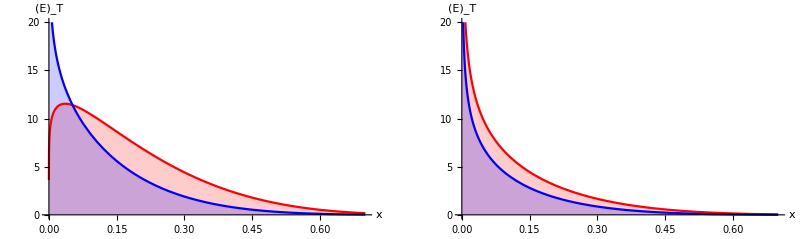

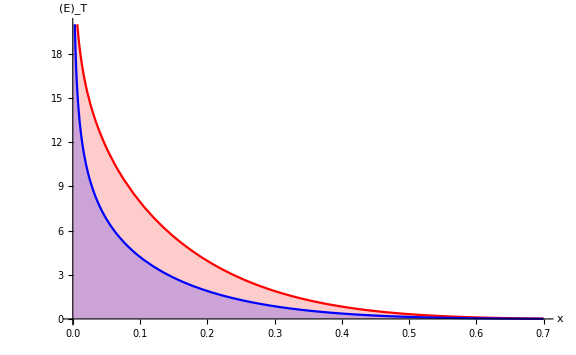
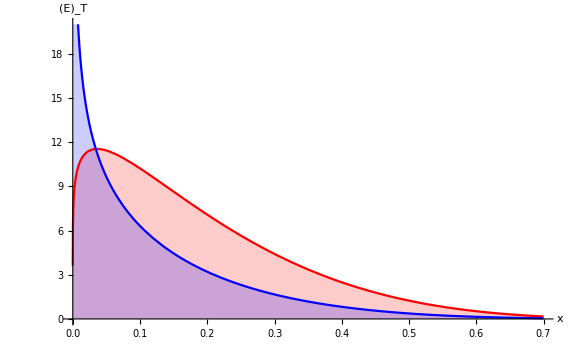

```mathematica
knu=4.82; kalphau=0.3;
knd=3.57; kalphad=0.3;
krollu[x_]:=knu(x^-kalphau(1-x)^4);
krolld[x_]:=knd(x^-kalphad(1-x)^5);


nu=22.0; alphau=-0.15;
nd=9.3; alphad=0.16;

snu=3.2; salphau=0.04;
snd=3.6; salphad=0.15;



fitu[n_,m_,x_]:=(nu+n*snu) x^-(alphau+m*salphau)(1-x)^4;
fitd[n_,m_,x_]:=(nd+n*snd) x^-(alphad+m*salphad)(1-x)^5;

kfitu[x_]:=22(x^0.15(1-x)^4);
kfitd[x_]:=9.3(x^-0.16(1-x)^5);

Print["Kroll      u-quarks = ",Integrate[krollu[a],{a,0,1}]]               
Print["Kroll      d-quarks = ",Integrate[krolld[a],{a,0,1}]]

Print["Global Fit u-quarks = ",Integrate[fitu[0,0,a],{a,0,1}]]      
Print["Global Fit d-quarks = ",Integrate[fitd[0,0,a],{a,0,1}]]

GraphicsGrid[{
{Plot[{fitu[0,0,x],fitd[0,0,x]},{x,-0.01,0.7},Filling->Axis,PlotRange->{0,20},ImageSize->Large,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}],Plot[{krollu[x],krolld[x]},{x,-0.01,0.7},Filling->Axis,PlotRange->{0,20},ImageSize->Large,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}]}},
ImageSize->Full,PlotLabel->Style[StandardForm[xz],FontSize->25,FontColor->Black]]

Plot[{fitu[0,0,x],krollu[x]},{x,-0.01,0.7},Filling->Axis,PlotRange->{0,20},ImageSize->Large,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}]Plot[{fitd[0,0,x],krolld[x]},{x,-0.01,0.7},Filling->Axis,PlotRange->{0,20},ImageSize->Large,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}]
```

```mathematica
Integrate[krollu[y],{y,0,1}]
```

2.07037

```mathematica
Plot[{fitu[x],fitd[x]},{x,0.01,0.7},Filling->Axis,PlotRange->{0,40},ImageSize->Large,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}]Plot[{krollu[x],krolld[x]},{x,0.01,0.7},Filling->Axis,PlotRange->{0,20},ImageSize->Large,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}]
```

```mathematica
Plot[{fitu[x],fitd[x]},{x,0.01,0.7},Filling->Axis,PlotRange->{0,40},ImageSize->Large,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}]Plot[{krollu[x],krolld[x]},{x,0.01,0.7},Filling->Axis,PlotRange->{0,20},ImageSize->Large,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"}]
```

```mathematica
Integrate[fitu[0,0,a],{a,0,1}]
Integrate[fitd[0,0,a],{a,0,1}]

Integrate[fitu[1,0,a],{a,0,1}]
Integrate[fitd[1,0,a],{a,0,1}]

Integrate[fitu[0,1,a],{a,0,1}]
Integrate[fitd[0,1,a],{a,0,1}]

Integrate[fitu[-1,0,a],{a,0,1}]
Integrate[fitd[-1,0,a],{a,0,1}]

Integrate[fitu[0,-1,a],{a,0,1}]
Integrate[fitd[0,-1,a],{a,0,1}]

Integrate[fitu[1,1,a],{a,0,1}]
Integrate[fitd[1,1,a],{a,0,1}]

Integrate[fitu[-1,-1,a],{a,0,1}]
Integrate[fitd[-1,-1,a],{a,0,1}]
```

3.17199

2.34239

3.63337

3.24912

3.45148

3.61297

2.71061

1.43566

2.92059

1.58856

3.95351

5.01154

2.49578

0.973635

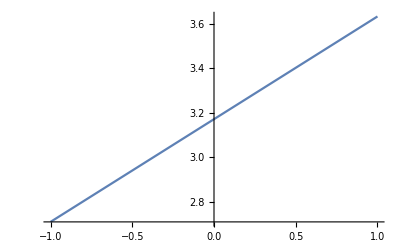

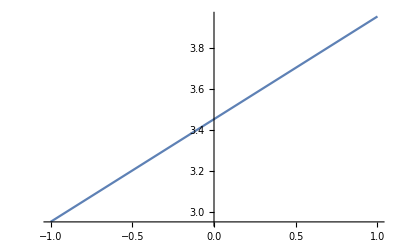

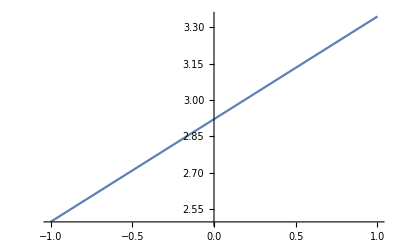

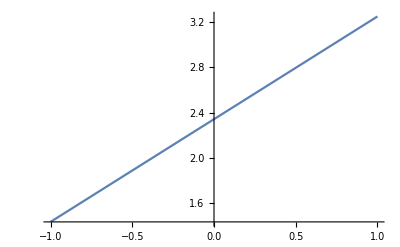

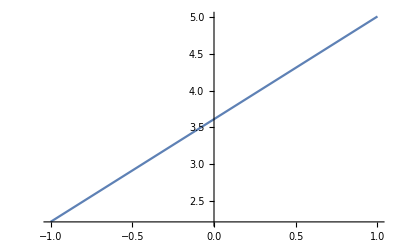

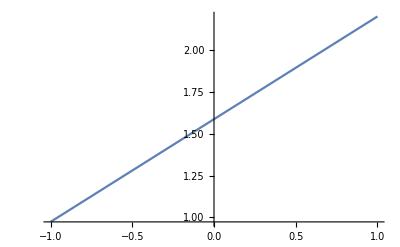

```mathematica
Plot[Integrate[fitu[x,0,a],{a,0,1}],{x,-1,1}]


Plot[Integrate[fitu[x,1,a],{a,0,1}],{x,-1,1}] 


Plot[Integrate[fitu[x,-1,a],{a,0,1}],{x,-1,1}]



 Plot[Integrate[fitd[x,0,a],{a,0,1}],{x,-1,1}]


Plot[Integrate[fitd[x,1,a],{a,0,1}],{x,-1,1}]


 Plot[Integrate[fitd[x,-1,a],{a,0,1}],{x,-1,1}]
```

```mathematica
plotfu=Plot3D[Integrate[fitu[n,m,a],{a,0,1}],{n,-1,1},{m,-1,1},
PlotLabel->Style[StandardForm["u quark"],FontSize->25,FontColor->Black],
PlotLegends->BarLegend[None], 
ColorFunction->"Rainbow",
PlotRange->All,Axes->True,AxesLabel->{n,m},
ImageSize->Large];
plotfu=Plot3D[Integrate[fitd[n,m,a],{a,0,1}],{n,-1,1},{m,-1,1},
PlotLabel->Style[StandardForm["d quark"],FontSize->25,FontColor->Black],
PlotLegends->BarLegend[None], 
ColorFunction->"Rainbow",
PlotRange->All,Axes->True,AxesLabel->{n,m},
ImageSize->Large];


GraphicsGrid[{{plotfu,plotfd}},ImageSize->Full]
```

-Graphics-